# Animal Sounds and Fourier Transforms

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/isaiahgalland/Desktop/230 Project

```mathematica
birdsound1 = Import["eagle.mp3"]
birdsound2= Import["cockatoo3.mp3"]
birdsound3 = Import["birdcall.mp3"]
bigcat1=Import["bigcat1.mp3"]
bigcat2=Import["bigcat2.mp3"]
bigcat3=Import["bigcat3.mp3"]
elephant=Import["elephant.mp3"]
mystery=Import["mystery.mp3"]
```

```mathematica
FTpart1[soundfile_]:=Module[{},
rate= soundfile//AudioSampleRate//QuantityMagnitude; (* samplerate in Hz *)
duration = soundfile//Duration//QuantityMagnitude ;(* duration in seconds *)
ampdata = soundfile//AudioData;
ampdata =  If[Length[Dimensions[ampdata]]>1,ampdata[[1]],ampdata];
samplenum =ampdata//Length; (* number of samples *)

timerange = duration; (* maximum time in seconds *)
timestep = duration/samplenum//N; (* time step in seconds *)
freqrange = rate/2//N; (* maximum frequency in Hz *)
freqstep=freqrange/samplenum//N; (* frequency step in Hz *)


chunksize =Min[1000,samplenum/50];
chunkcount = Min[Floor[samplenum/chunksize],50];
ListAnimate[Table[ListPlot[ampdata[[(n-1)*chunksize+1;;n*chunksize]],Joined->True,Frame->True,PlotRange->All],{n,1,chunkcount}]];
]
```

```mathematica
FTpart1[birdsound2]
```

Part::span: 1;;17856/25 is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

ListPlot::lpn: {0.,8.70714×10^-14,5.25482×10^-14,8.26461×10^-14,6.73638×10^-14,-5.5393×10^-14,-1.94132×10^-13,«37»,-5.34989×10^-11,-8.34126×10^-11,-3.69695×10^-11,5.49701×10^-11,1.11876×10^-10,7.23029×10^-11,«35662»}⟦1;;(«5»)/25⟧ is not a list of numbers or pairs of numbers.

Part::span: 17881/25;;35712/25 is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

ListPlot::lpn: {0.,8.70714×10^-14,5.25482×10^-14,8.26461×10^-14,6.73638×10^-14,-5.5393×10^-14,-1.94132×10^-13,«37»,-5.34989×10^-11,-8.34126×10^-11,-3.69695×10^-11,5.49701×10^-11,1.11876×10^-10,7.23029×10^-11,«35662»}⟦(«5»)/25;;(«5»)/(«2»)⟧ is not a list of numbers or pairs of numbers.

Part::span: 35737/25;;53568/25 is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

General::stop: Further output of Part::span will be suppressed during this calculation.

ListPlot::lpn: {0.,8.70714×10^-14,5.25482×10^-14,8.26461×10^-14,6.73638×10^-14,-5.5393×10^-14,-1.94132×10^-13,«37»,-5.34989×10^-11,-8.34126×10^-11,-3.69695×10^-11,5.49701×10^-11,1.11876×10^-10,7.23029×10^-11,«35662»}⟦(«5»)/25;;(«5»)/(«2»)⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

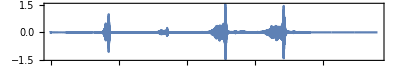

18986.5

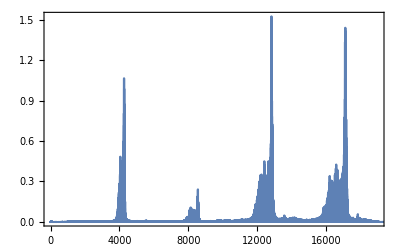

```mathematica
rawspectrum = FourierDCT[ampdata]; (* raw discrete Fourier transform *)
ListPlot[rawspectrum,Joined->True,Frame->True,DataRange->{0,freqrange},PlotRange->All,AspectRatio->1/6]

goodrange[rawspectraldata_,threshold_] := Module[{len,absdata,maxabs,blocksize,blockmaxvals,maxresiduals,threshhold,maxlargenough,falsepositions,cutoff},
len = rawspectraldata//Length;
absdata = rawspectraldata//Abs;
maxabs=absdata//Abs//Max;
blocksize =Min[Ceiling[len/10000],100];
blockmaxvals =Max/@Partition[absdata,blocksize];
maxresiduals = Table[blockmaxvals[[i;;]]//Max,{i,Length[blockmaxvals]}];
maxlargenough=(#>maxabs*threshold)&/@maxresiduals;
falsepositions = Position[maxlargenough,False];
cutoff = If[Length[falsepositions]>0,Min[1.1*falsepositions[[1,1]]*blocksize//Ceiling,samplenum],samplenum];
cutoff*freqstep
]
freqmax = goodrange[rawspectrum,0.05]
ListPlot[rawspectrum//Abs,Joined->True,Frame->True,DataRange->{0,freqrange},PlotRange->{{1,freqmax},All}]
```

```mathematica
(*FTpart1[#]&/@soundlist
```

```mathematica
(*freqmax = goodrange[rawspectrum,0.05]
(* Plot the abs value of the spectrum. If you don't like the freqmax value obtained above, set it to whatever you prefer. *)
ListPlot[rawspectrum//Abs,Joined->True,Frame->True,DataRange->{0,freqrange},PlotRange->{{1,freqmax},All}]
```

```mathematica
(*FTpart1[#]&/@soundlist
```

```mathematica
(*rawspectrum = FourierDCT[ampdata]; (* raw discrete Fourier transform *)
ListPlot[rawspectrum,Joined->True,Frame->True,DataRange->{0,freqrange},PlotRange->All,AspectRatio->1/6]

goodrange[rawspectraldata_,threshold_] := Module[{len,absdata,maxabs,blocksize,blockmaxvals,maxresiduals,threshhold,maxlargenough,falsepositions,cutoff},
len = rawspectraldata//Length;
absdata = rawspectraldata//Abs;
maxabs=absdata//Abs//Max;
blocksize =Min[Ceiling[len/10000],100];
blockmaxvals =Max/@Partition[absdata,blocksize];
maxresiduals = Table[blockmaxvals[[i;;]]//Max,{i,Length[blockmaxvals]}];
maxlargenough=(#>maxabs*threshold)&/@maxresiduals;
falsepositions = Position[maxlargenough,False];
cutoff = If[Length[falsepositions]>0,Min[1.1*falsepositions[[1,1]]*blocksize//Ceiling,samplenum],samplenum];
cutoff*freqstep
]
freqmax = goodrange[rawspectrum,0.05]

(* Plot the abs value of the spectrum. If you don't like the freqmax value obtained above, set it to whatever you prefer. *)
ListPlot[rawspectrum//Abs,Joined->True,Frame->True,DataRange->{0,freqrange},PlotRange->{{1,freqmax},All}]
```